```mathematica
++
```

## Simplifying Expressions, Series, and Replacement Rules

```mathematica
x=5
```

5

Clear eliminates previous values assigned to variables.  A cleared variable shows up in blue.

```mathematica
Clear[x]
```

```mathematica
Sin[x]^2+Cos[x]^2
```

Cos[x]^2+Sin[x]^2

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

FullSimplify will try harder than simplify to make the expression compact.  It can often take longer to run.

```mathematica
FullSimplify[Sin[x]^2+Cos[x]^2]
```

1

calling argument//function is equivalent notation to function[argument]

```mathematica
Sin[x]^2+Cos[x]^2//FullSimplify
```

1

Series is a useful function for Taylor expanding in small quantities

```mathematica
Series[Exp[-x^2/a^2],{x,0,2}]
```

1-x^2/a^2+O[x]^3

```mathematica
Series[Exp[-x^2/a^2],{x,0,4}]
```

1-x^2/a^2+x^4/(2 a^4)+O[x]^5

```mathematica
Series[Exp[-(x-1)^2/a^2],{x,1,4}]
```

1-(x-1)^2/a^2+(x-1)^4/(2 a^4)+O[x-1]^5

notation [[i]] takes the ith element from an object.  Calling Series generates an object containing the small variable as the first element, the point expanded around as the second element, and the expansion coefficients as the third element.

```mathematica
Series[Exp[-(x-1)^2/a^2],{x,1,4}][[1]]
```

x

```mathematica
Series[Exp[-(x-1)^2/a^2],{x,1,4}][[2]]
```

1

```mathematica
Series[Exp[-(x-1)^2/a^2],{x,1,4}][[3]]
```

{1,0,-1/a^2,0,1/(2 a^4)}

/.{replacement rules} can be used to replace variables in an expression

```mathematica
Sin[x]/.{x->2}
```

Sin[2]

```mathematica
Sin[x+b]/.{x->2,b->q}
```

Sin[2+q]

//N numerically evaluates an expression

```mathematica
(2*π)/(698*10^-9)
```

(1000000000 π)/349

```mathematica
(2*π)/(698*10^-9)//N
```

9.0017×10^6

Expand breaks out an expression into individual terms

```mathematica
a*(b+c+d)
```

a (b+c+d)

```mathematica
a*(b+c+d)//Expand
```

a b+a c+a d

## Differentiation and Integration

```mathematica
D[x^5,x]
```

5 x^4

```mathematica
D[x^5,{x,2}]
```

20 x^3

```mathematica
D[x^5*y,{x,2}]
```

20 x^3 y

```mathematica
D[D[x^5*y,{x,2}],y]
```

20 x^3

```mathematica
Integrate[x^5,x]
```

x^6/6

```mathematica
Integrate[x^5,{x,1,a}]
```

-1/6+a^6/6

can specify assumptions for integrals

```mathematica
Integrate[Exp[-x^2/(2*σ^2)],{x,-∞,∞}]
```

ConditionalExpression[(√(2 π))/(√(1/σ^2)),Re[σ^2]>0]

```mathematica
Integrate[Exp[-x^2/(2*σ^2)],{x,-∞,∞},Assumptions->{σ>0}]
```

√(2 π) σ

can also numerically integrate

```mathematica
Integrate[(Sin[x]/x)^3,{x,0,5}]//N
```

1.17863

```mathematica
NIntegrate[(Sin[x]/x)^3,{x,0,5}]
```

1.17863

can carry out Fourier transform

```mathematica
FourierTransform[ⅇ^(-t^2),t,ω]
```

(ⅇ^(-ω^2/4))/(√2)

inverse Fourier transform

```mathematica
InverseFourierTransform[(ⅇ^(-ω^2/4))/(√2),ω,t]
```

ⅇ^(-t^2)

## Solving equations and differential equations

```mathematica
sol=Solve[1/2*g*T^2==h,T]
```

{{T→-(√2 √h)/(√g)},{T→(√2 √h)/(√g)}}

```mathematica
T/.sol[[2]]
```

(√2 √h)/(√g)

DSolve solves differential equations.  Example: solve Euler-Lagrange equation for uniform gravitational field.  Use functions with explicit arguments and primes for their derivatives, as done below with z[t] and z’[t].

```mathematica
L=1/2*m*z'[t]^2-m*g*z[t]
```

-g m z[t]+1/2 m z'[t]^2

```mathematica
eqn=D[D[L,z'[t]],t]==D[L,z[t]]
```

m z''[t]==-g m

can solve for general case, leaving coefficients to be determined by initial conditions

```mathematica
DSolve[eqn,z[t],t]
```

{{z[t]→-(g t^2)/2+C[1]+t C[2]}}

can explicitly add initial conditions

```mathematica
initial={z'[0]==vz0,z[0]==z0}
```

{z'[0]==vz0,z[0]==z0}

Join puts together two lists (have to put brackets around eqn to make it into a list)

```mathematica
eqnJoinInitial=Join[{eqn},initial]
```

{m z''[t]==-g m,z'[0]==vz0,z[0]==z0}

```mathematica
sol=DSolve[eqnJoinInitial,z[t],t]//Expand
```

{{z[t]→-(g t^2)/2+t vz0+z0}}

```mathematica
z[t]/.sol[[1]]
```

-(g t^2)/2+t vz0+z0

repeat with a gravity gradient

```mathematica
L=1/2*m*z'[t]^2-m*g*z[t]-1/2*m*Tzz*z[t]^2
```

-g m z[t]-1/2 m Tzz z[t]^2+1/2 m z'[t]^2

```mathematica
eqn=D[D[L,z'[t]],t]==D[L,z[t]]
```

m z''[t]==-g m-m Tzz z[t]

can solve for general case, leaving coefficients to be determined by initial conditions

```mathematica
FullSimplify[DSolve[eqn,z[t],t]]
```

```mathematica
{{z[t]->-g/Tzz+C[1] Cos[t √Tzz]+C[2] Sin[t √Tzz]}}
```

{{z[t]→-g/Tzz+C[1] Cos[t √Tzz]+C[2] Sin[t √Tzz]}}

can explicitly add initial conditions

```mathematica
initial={z'[0]==vz0,z[0]==z0}
```

{z'[0]==vz0,z[0]==z0}

Join puts together two lists (have to put brackets around eqn to make it into a list)

```mathematica
eqnJoinInitial=Join[{eqn},initial]
```

{m z''[t]==-g m-m Tzz z[t],z'[0]==vz0,z[0]==z0}

```mathematica
sol=DSolve[eqnJoinInitial,z[t],t]//Expand
```

{{z[t]→-g/Tzz+(g Cos[t √Tzz])/Tzz+z0 Cos[t √Tzz]+(vz0 Sin[t √Tzz])/(√Tzz)}}

```mathematica
z[t]/.sol[[1]]
```

-g/Tzz+(g Cos[t √Tzz])/Tzz+z0 Cos[t √Tzz]+(vz0 Sin[t √Tzz])/(√Tzz)

```mathematica
z[t]/.sol[[1]]/.{Tzz->-Γ}//FullSimplify
```

(g+(-g+z0 Γ) Cosh[t √Γ]+vz0 √Γ Sinh[t √Γ])/Γ

NDSolve can numerically solve differential equations, generates an interpolating function object

```mathematica
ndsol=NDSolve[{z''[t]==Sin[z[t]],z[0]==1,z'[0]==0},z,{t,0,100}]
```

{{z→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
z[1]/.ndsol[[1]]
```

1.43729

```mathematica
z'[1]/.ndsol[[1]]
```

0.902431

Plot solution

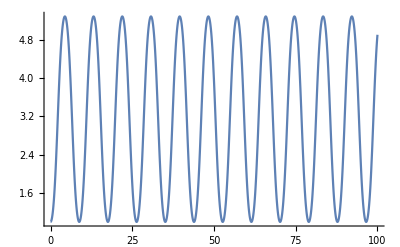

```mathematica
Plot[z[t]/.ndsol[[1]],{t,0,100}]
```

can also numerically intregrate

```mathematica
Integrate[x^3*Sin[x],{x,0,10}]
```

-940 Cos[10]+294 Sin[10]

```mathematica
Integrate[x^3*Sin[x],{x,0,10}]//N
```

628.785

```mathematica
NIntegrate[x^3*Sin[x],{x,0,10}]
```

628.785

## Conditionals

Can define piecewise functions using the If function (can query attributes of a function by typing ??function)

```mathematica
??If
```

If[condition,t,f] gives t if condition evaluates to True, and f if it evaluates to False. 
If[condition,t,f,u] gives u if condition evaluates to neither True nor False.

Attributes[If]={HoldRest,Protected}

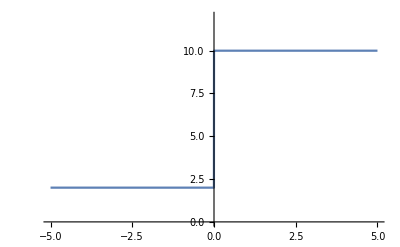

```mathematica
Plot[If[x>0,10,2],{x,-5,5},PlotRange->{0,12}]
```

## Typesetting

escape letter escape generates Greek letters.  For example, with d:

```mathematica
δ
```

δ

“e” is escape e e escape

```mathematica
ⅇ
```

ⅇ

ℏ is escape h b escape

```mathematica
ℏ
```

ℏ

control + ^ allows convenient exponential typesetting

```mathematica
ⅇ^2//N
```

7.38906

control + / allows nice fraction typesetting

```mathematica
a/b
```

a/b